```mathematica
Now
```

Fri 29 Jan 2021 08:47:01GMT-5.

Consider the ellipse given by x^2/16 + y^2/36 = 1. Generate the curve with 3 different M-environments.

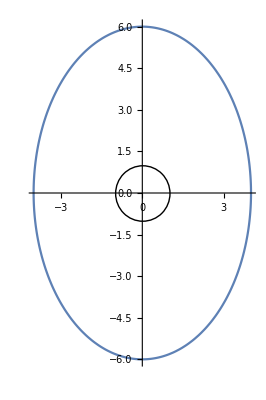

```mathematica
ParametricPlot[
{4Cos[t],6Sin[t]},
{t,0,2Pi},
Epilog->Circle[]
]
```

```mathematica
Solve[
x^2/16+y^2/36==1,
y
]
```

{{y→-3/2 √(16-x^2)},{y→(3 √(16-x^2))/2}}

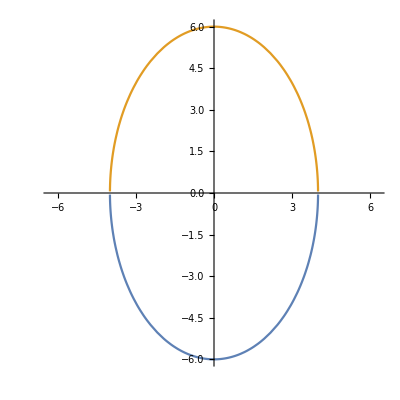

```mathematica
Plot[
{-3/2 √(16-x^2),(3 √(16-x^2))/2},
{x,-2Pi,2Pi},
AspectRatio->1
]
```

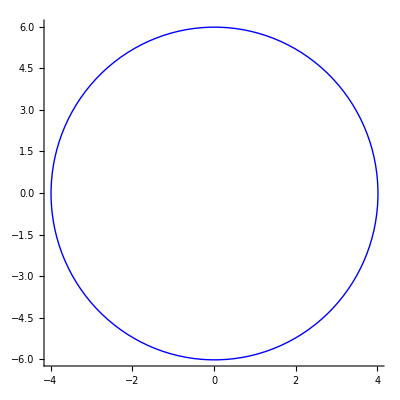

```mathematica
Graphics[
{
Blue,Circle[{0,0},{4,6}]
},
Axes->True,
AspectRatio->1
]
```

```mathematica
Now
```

Fri 5 Feb 2021 12:47:51GMT-5.

Let’s generate a scaled version of the moon’s orbit around the earth. Wee need the radii of the moon & earth

```mathematica
Graphics[
{

},
Axes->True
]
```

```mathematica
Now
```

Wed 10 Feb 2021 08:35:04GMT-5.

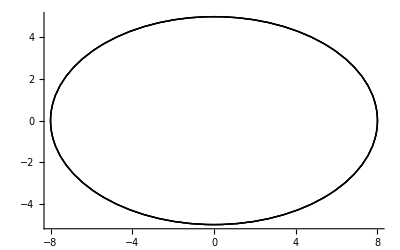

```mathematica
Graphics[
{Circle[{0,0},{8,5}],
Rotate[
Circle[{0,0},{8,5}],(*thing to rotate*)
Pi/9,(*amount of rotation*)
{0,0}(*center of rotation*)
],
Rotate[
Circle[{0,0},{8,5}],(*thing to rotate*)
2Pi/9,(*amount of rotation*)
{0,0}(*center of rotation*)
]
},
Axes->True
]
```

Make an ellipse”flower”by spacing enough ellipses at 20.ba intervals to wrap completely around the origin.

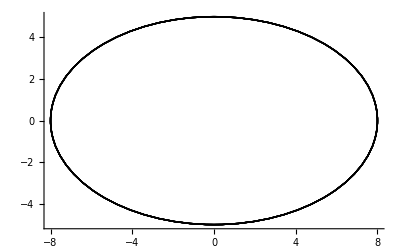

```mathematica
Graphics[
{
Table[
Rotate[
Circle[{0,0},{8,5}],(*thing to rotate*)
k Pi/9,(*amount of rotation*)
{0,0}(*center of rotation*)
],
{k,0,8,1}
]
},
Axes->True
]
```

Turn this logic into a function ellipses[a,b,number] that draws the given number of a by b ellipses, rotated appropriately.

```mathematica
ellipses[a_,b_,number_]:=
Graphics[
Table[
Rotate[
{Hue[k/number],Thick,Circle[{0,0},{a,b}]},(*thing to rotate*)
k Pi/number,(*amount of rotation*)
{0,0}(*center of rotation*)
],
{k,0,number-1,1}
]
]
```

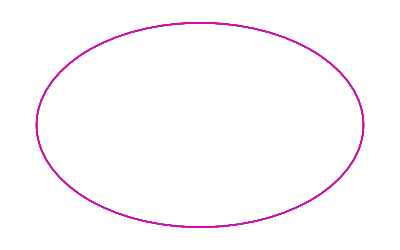

```mathematica
ellipses[8,5,10]
```

```mathematica
Now
```

Wed 17 Feb 2021 11:17:43GMT-5.

In class notes, we thought about the hyperbolas
(y-3)^2/25-(x+2)^2/9 = 1 AND
(x+2)^2/9 - (y-3)^2/25 = 1
plot ‘em both

```mathematica
Solve[
(y-3)^2/25-(x+2)^2/9==1,
y
]
```

{{y→1/3 (9-5 √(13+4 x+x^2))},{y→1/3 (9+5 √(13+4 x+x^2))}}

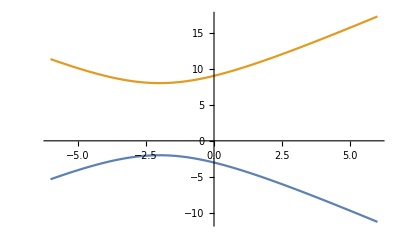

```mathematica
Plot[
{1/3 (9-5 √(13+4 x+x^2)),1/3 (9+5 √(13+4 x+x^2))},
{x,-6,6}
]
```

```mathematica
Solve[
(x+2)^2/9-(y-3)^2/25==1,
y
]
```

{{y→1/3 (9-5 √(-5+4 x+x^2))},{y→1/3 (9+5 √(-5+4 x+x^2))}}

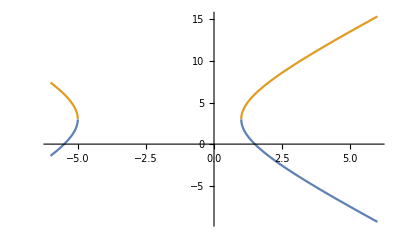

```mathematica
Plot[
{1/3 (9-5 √(-5+4 x+x^2)),1/3 (9+5 √(-5+4 x+x^2))},
{x,-6,6}
]
```

```mathematica
Map[
y/.#&,
Flatten[
Map[
Solve[#,y]&,
{
(y-3)^2/25-(x+2)^2/9==1,
(x+2)^2/9-(y-3)^2/25==1
}
]
]
]
```

{1/3 (9-5 √(13+4 x+x^2)),1/3 (9+5 √(13+4 x+x^2)),1/3 (9-5 √(-5+4 x+x^2)),1/3 (9+5 √(-5+4 x+x^2))}

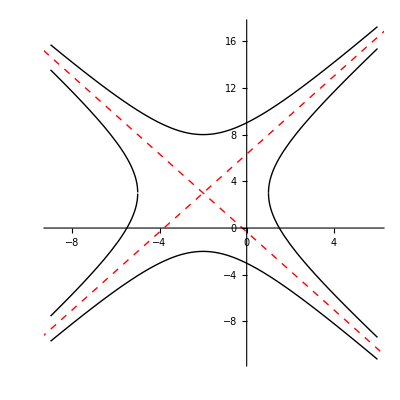

```mathematica
Plot[
{1/3 (9-5 √(13+4 x+x^2)),1/3 (9+5 √(13+4 x+x^2)),1/3 (9-5 √(-5+4 x+x^2)),1/3 (9+5 √(-5+4 x+x^2))},
{x,-9,6},
AspectRatio->1,
PlotStyle->Directive[{Black,Thick}],
Epilog->{
Opacity @0, EdgeForm[{Red,Dashed}],
Rectangle[{-5,-2},{1,8}],
Red,Dashed,Opacity@1,
InfiniteLine[{{-5,-2},{1,8}}],
InfiniteLine[{-2,3},{-3,5}]
}
]
```

```mathematica
Now
```

Thu 18 Feb 2021 13:41:29GMT-5.

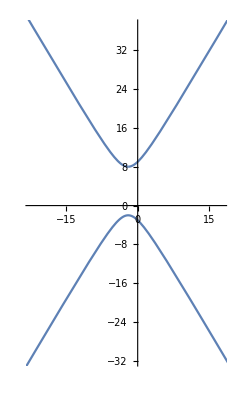

```mathematica
ParametricPlot[
{3Tan[t]-2,5Sec[t]+3},
{t,0,2Pi},
PlotRange->{{},{}}
]
```

```mathematica
Now
```

Fri 26 Feb 2021 10:51:11GMT-5.

```mathematica
Manipulate[
ParametricPlot[
{
(R+r)Cos[x]-r Cos[(R+r)x/r],
(R+r)Sin[x]-r Sin[(R+r)x/r]
},
{x,0,z},
PlotRange-> 2 R+r+1,
PlotPoints->100
],
{R,2,10,1,Appearance->"Labeled"},
{r,1,R-1,1,Appearance->"Labeled"},
{z,0.0001,2 r Pi/GCD[r,R],Appearance->"Labeled"}
]
```

```mathematica
Now
```

Mon 1 Mar 2021 11:10:09GMT-5.

start plotting curves in polar coordinates

```mathematica
points=
Table[
{t,N[1-2Cos[t]]},
{t,0,2Pi,Pi/12}
]
```

{{0,-1.},{π/12,-0.931852},{π/6,-0.732051},{π/4,-0.414214},{π/3,0.},{(5 π)/12,0.482362},{π/2,1.},{(7 π)/12,1.51764},{(2 π)/3,2.},{(3 π)/4,2.41421},{(5 π)/6,2.73205},{(11 π)/12,2.93185},{π,3.},{(13 π)/12,2.93185},{(7 π)/6,2.73205},{(5 π)/4,2.41421},{(4 π)/3,2.},{(17 π)/12,1.51764},{(3 π)/2,1.},{(19 π)/12,0.482362},{(5 π)/3,0.},{(7 π)/4,-0.414214},{(11 π)/6,-0.732051},{(23 π)/12,-0.931852},{2 π,-1.}}

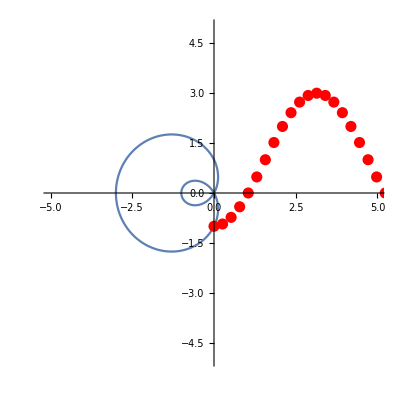

```mathematica
PolarPlot[
1-2Cos[t],
{t,0,2Pi},
PlotRange->5,
Epilog->{
Red,PointSize[0.02],
Point[points]
}
]
```

```mathematica
Now
```

Tue 2 Mar 2021 13:37:57GMT-5.

```mathematica
Table[
{t,N[2+2Sin[t]]},
{t,0,2Pi,Pi/12}
]//TableForm
```

0 | 2.
π/12 | 2.51764
π/6 | 3.
π/4 | 3.41421
π/3 | 3.73205
(5 π)/12 | 3.93185
π/2 | 4.
(7 π)/12 | 3.93185
(2 π)/3 | 3.73205
(3 π)/4 | 3.41421
(5 π)/6 | 3.
(11 π)/12 | 2.51764
π | 2.
(13 π)/12 | 1.48236
(7 π)/6 | 1.
(5 π)/4 | 0.585786
(4 π)/3 | 0.267949
(17 π)/12 | 0.0681483
(3 π)/2 | 0.
(19 π)/12 | 0.0681483
(5 π)/3 | 0.267949
(7 π)/4 | 0.585786
(11 π)/6 | 1.
(23 π)/12 | 1.48236
2 π | 2.

```mathematica
Manipulate[
ParametricPlot[
{
(R+r)Cos[x]-r Cos[(R+r)x/r],
(R+r)Sin[x]-r Sin[(R+r)x/r]
},
{x,0,z},
PlotRange-> 2 r+R+1,
PlotPoints->100,
PlotStyle->Black,
Axes->False,
Epilog->{
EdgeForm[{Black,Thin}],LightBlue,Disk[{0,0},R],
LightPink,Disk[{(R+r)Cos[z],(R+r)Sin[z]},r],
Black,PointSize@0.02,Point[{(R+r)Cos[z]-r Cos[(R+r)z/r],(R+r)Sin[z]-r Sin[(R+r)z/r]}]
}
],
{{R,11},2,12,1,Appearance->"Labeled"},
{{r,6},1,R-1,1,Appearance->"Labeled"},
{{z,37},0.0001,2 r Pi/GCD[r,R],Appearance->"Labeled"}
]
```

```mathematica
Now
```

Wed 3 Mar 2021 13:59:38GMT-5.

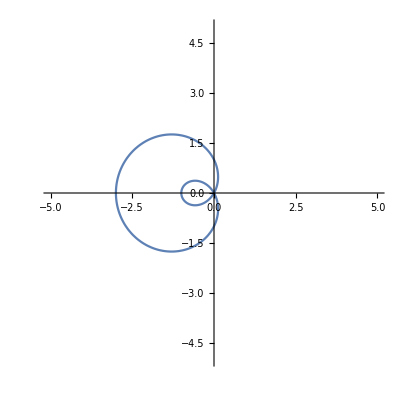

```mathematica
ParametricPlot[
{(1-2Cos[t]) Cos[t],(1-2Cos[t]) Sin[t]},
{t,0,2Pi},
PlotRange->5,
Epilog->{
Red,PointSize[0.02]
}
]
```

```mathematica
Now
```

Mon 8 Mar 2021 08:37:54GMT-5.

```mathematica
Manipulate[
Row[{

PolarPlot[
Sin[2x]+Cos[4x],
{x,0,t},
PlotRange->1.6,
PlotStyle->Black,
ImageSize->{250,250},
Ticks->{{1.5,-1.5},{1.5,-1.5}},
Epilog->{
PointSize[0.03],Red,
Point[
Table[
{
(Sin[2x]+Cos[4x])Cos[x],
(Sin[2x]+Cos[4x])Sin[x]
},
{x,0,2Pi,Pi/12}
]
],
Line[{{(Sin[2t]+Cos[4t])Cos[t],(Sin[2t]+Cos[4t])Sin[t]},{0,0}}]
}
],

Plot[
Sin[2x]+Cos[4x],
{x,0,t},
PlotRange->{{-.1,2Pi+.1},{1.3,-2.1}},
PlotStyle->Black,
ImageSize->{500,250},
Ticks->{Range[0,2Pi,Pi/2],{1,-1,-2}},
Epilog->{
PointSize[0.02],Red,
Opacity[0.4],
Point[
Table[
{x,Sin[2x]+Cos[4x]},
{x,0,2Pi,Pi/12}
]
],
Opacity[1],
Line[{{t,0},{t,Sin[2t]+Cos[4t]}}]
}
]
}],
{{t,5.9},0.0001,2Pi,Appearance->"Labeled"}
]
```

```mathematica
Now
```

Tue 9 Mar 2021 08:34:33GMT-5.

```mathematica
Manipulate[
PolarPlot[
a+b f[x],
{x,0,2Pi},
PlotStyle->Black,
PlotRange->21,
Epilog->{
PointSize[0.02],
Point[
Table[
{(a+b f[x])Cos[x],(a+b f[x])Sin[x]},
{x,0,2Pi,Pi/12}
]
]
}
],
{{a,7},1,10,Appearance->"Labeled"},
{{b,10},1,10,Appearance->"Labeled"},
{{f,Sin},{Cos,Sin}}
]
```

```mathematica
TableForm[
Table[
Labeled[
PolarPlot[
{Cos[a x] Sin[b x]},
{x,0,2Pi},
ImageSize->{60,60},
PlotRange->1,
Ticks->None,
PlotStyle->{Black,Thin}
],
Row[{"r = sin(",b θ, ") cos(",a θ,")"}],
LabelStyle->Directive[Italic,FontSize->5]
],
{a,1,7,1},
{b,1,7,1}
],
TableSpacing->{0,1}
]
```

-Graphics-r = sin(θ) cos(θ) | -Graphics-r = sin(2 θ) cos(θ) | -Graphics-r = sin(3 θ) cos(θ) | -Graphics-r = sin(4 θ) cos(θ) | -Graphics-r = sin(5 θ) cos(θ) | -Graphics-r = sin(6 θ) cos(θ) | -Graphics-r = sin(7 θ) cos(θ)
-Graphics-r = sin(θ) cos(2 θ) | -Graphics-r = sin(2 θ) cos(2 θ) | -Graphics-r = sin(3 θ) cos(2 θ) | -Graphics-r = sin(4 θ) cos(2 θ) | -Graphics-r = sin(5 θ) cos(2 θ) | -Graphics-r = sin(6 θ) cos(2 θ) | -Graphics-r = sin(7 θ) cos(2 θ)
-Graphics-r = sin(θ) cos(3 θ) | -Graphics-r = sin(2 θ) cos(3 θ) | -Graphics-r = sin(3 θ) cos(3 θ) | -Graphics-r = sin(4 θ) cos(3 θ) | -Graphics-r = sin(5 θ) cos(3 θ) | -Graphics-r = sin(6 θ) cos(3 θ) | -Graphics-r = sin(7 θ) cos(3 θ)
-Graphics-r = sin(θ) cos(4 θ) | -Graphics-r = sin(2 θ) cos(4 θ) | -Graphics-r = sin(3 θ) cos(4 θ) | -Graphics-r = sin(4 θ) cos(4 θ) | -Graphics-r = sin(5 θ) cos(4 θ) | -Graphics-r = sin(6 θ) cos(4 θ) | -Graphics-r = sin(7 θ) cos(4 θ)
-Graphics-r = sin(θ) cos(5 θ) | -Graphics-r = sin(2 θ) cos(5 θ) | -Graphics-r = sin(3 θ) cos(5 θ) | -Graphics-r = sin(4 θ) cos(5 θ) | -Graphics-r = sin(5 θ) cos(5 θ) | -Graphics-r = sin(6 θ) cos(5 θ) | -Graphics-r = sin(7 θ) cos(5 θ)
-Graphics-r = sin(θ) cos(6 θ) | -Graphics-r = sin(2 θ) cos(6 θ) | -Graphics-r = sin(3 θ) cos(6 θ) | -Graphics-r = sin(4 θ) cos(6 θ) | -Graphics-r = sin(5 θ) cos(6 θ) | -Graphics-r = sin(6 θ) cos(6 θ) | -Graphics-r = sin(7 θ) cos(6 θ)
-Graphics-r = sin(θ) cos(7 θ) | -Graphics-r = sin(2 θ) cos(7 θ) | -Graphics-r = sin(3 θ) cos(7 θ) | -Graphics-r = sin(4 θ) cos(7 θ) | -Graphics-r = sin(5 θ) cos(7 θ) | -Graphics-r = sin(6 θ) cos(7 θ) | -Graphics-r = sin(7 θ) cos(7 θ)

```mathematica
Table[
{x,N@1+2Sin[x]},
{x,0,2Pi,Pi/12}
]
```

{{0,1.},{π/12,1.51764},{π/6,2.},{π/4,2.41421},{π/3,2.73205},{(5 π)/12,2.93185},{π/2,3.},{(7 π)/12,2.93185},{(2 π)/3,2.73205},{(3 π)/4,2.41421},{(5 π)/6,2.},{(11 π)/12,1.51764},{π,1.},{(13 π)/12,0.482362},{(7 π)/6,0.},{(5 π)/4,-0.414214},{(4 π)/3,-0.732051},{(17 π)/12,-0.931852},{(3 π)/2,-1.},{(19 π)/12,-0.931852},{(5 π)/3,-0.732051},{(7 π)/4,-0.414214},{(11 π)/6,0.},{(23 π)/12,0.482362},{2 π,1.}}

```mathematica
Now
```

Mon 15 Mar 2021 13:31:43GMT-4.

superTrig09 HW labels:

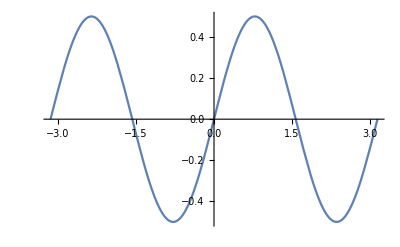
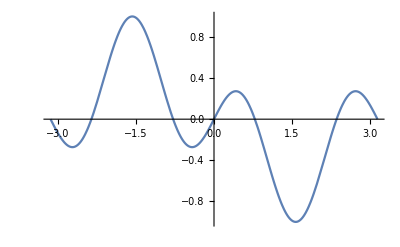
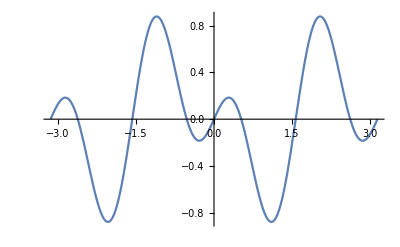
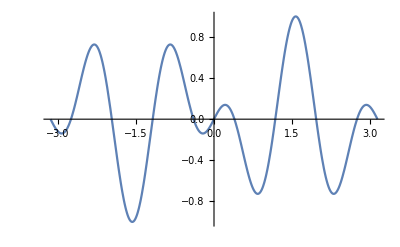
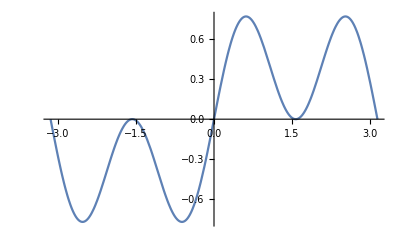
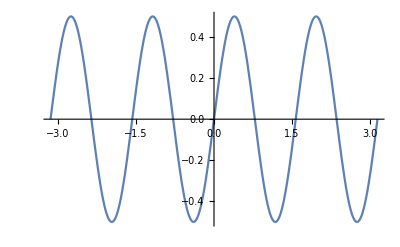
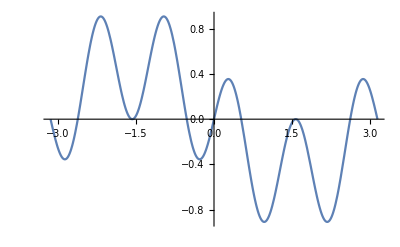
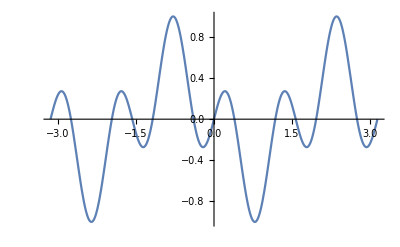
-Graphics-part1part2part3 | -Graphics-part1part2part3 | -Graphics-part1part2part3 | -Graphics-part1part2part3
-Graphics-part1part2part3 | -Graphics-part1part2part3 | -Graphics-part1part2part3 | -Graphics-part1part2part3
-Graphics-part1part2part3 | -Graphics-part1part2part3 | -Graphics-part1part2part3 | -Graphics-part1part2part3
-Graphics-part1part2part3 | -Graphics-part1part2part3 | -Graphics-part1part2part3 | -Graphics-part1part2part3

```mathematica
TableForm[
Table[
Labeled[
Plot[
Sin[a x]Cos[b x],
{x,-Pi,Pi}
],
Row[{part1,part2,part3}]
],
{a,1,4,1},
{b,1,4,1}
]
]
```

```mathematica
Now
```

Thu 18 Mar 2021 08:58:35GMT-4.

```mathematica
RowReduce[
{
{1,1,1,-3},
{2,-3,2,9},
{4,1,-3,11}
}
]
```

{{1,0,0,2},{0,1,0,-3},{0,0,1,-2}}

```mathematica
MatrixForm[%]
```

(1 | 0 | 0 | 2
0 | 1 | 0 | -3
0 | 0 | 1 | -2)

```mathematica
Clear[x]
Clear[y]
Clear[z]
```

```mathematica
{
{1,1,1},
{2,-3,2},
{4,1,-3}
}.{x,y,z}
```

{x+y+z,2 x-3 y+2 z,4 x+y-3 z}

```mathematica
7x = 28
(1/7)7x = (1/7)28
```

```mathematica
Inverse[
{
{1,1,1},
{2,-3,2},
{4,1,-3}
}
]
```

{{1/5,4/35,1/7},{2/5,-1/5,0},{2/5,3/35,-1/7}}

```mathematica
Inverse[%]
```

{{1,1,1},{2,-3,2},{4,1,-3}}

```mathematica
{{1,1,1},{2,-3,2},{4,1,-3}}.{{1/5,4/35,1/7},{2/5,-1/5,0},{2/5,3/35,-1/7}}
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
MatrixForm@%
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
h = RandomInteger[{-1,7},{20,20}];
```

```mathematica
MatrixForm@h
```

(2 | 6 | 5 | 5 | 6 | 3 | 6 | 5 | 1 | 1 | -1 | 2 | 2 | -1 | 0 | 7 | 1 | 3 | -1 | 7
3 | 4 | 0 | 6 | -1 | -1 | 0 | 6 | -1 | 5 | 3 | -1 | 5 | 0 | 5 | 1 | 0 | -1 | 3 | 1
-1 | 3 | -1 | 6 | 2 | 2 | 7 | 0 | -1 | 0 | 4 | 1 | -1 | 1 | -1 | 6 | -1 | 4 | 4 | 3
7 | 0 | 7 | 5 | 3 | -1 | 1 | 4 | -1 | 7 | 3 | 3 | 6 | 1 | 4 | 3 | -1 | -1 | 1 | 4
4 | 6 | 2 | 6 | 1 | -1 | 4 | 2 | 6 | 3 | 4 | 4 | 1 | 3 | -1 | 6 | 1 | 1 | 5 | 3
0 | 1 | 7 | 0 | 6 | 5 | 5 | 0 | 3 | -1 | 3 | 1 | 3 | 2 | 5 | 5 | 2 | 3 | 5 | 2
0 | 4 | 2 | -1 | 5 | 4 | 2 | 4 | 1 | -1 | -1 | 1 | 5 | 1 | 0 | 2 | 3 | 5 | 1 | 7
3 | 0 | 1 | -1 | 7 | 3 | 1 | 1 | 0 | 6 | 5 | 1 | 7 | 7 | 5 | 2 | 1 | 3 | 5 | 1
2 | 3 | 0 | -1 | 3 | 5 | 6 | 1 | 3 | 2 | 5 | 4 | 6 | 5 | 1 | 0 | 5 | 3 | 0 | 1
5 | 3 | 3 | 6 | 4 | 1 | 4 | 4 | 7 | -1 | 7 | 3 | 7 | 1 | 5 | 0 | 2 | 3 | -1 | 1
1 | 0 | 6 | 7 | -1 | 0 | 6 | 5 | 5 | 7 | 4 | 1 | 1 | 3 | 7 | -1 | 4 | 7 | 4 | 0
6 | 1 | 3 | 6 | 2 | 1 | 1 | 2 | 1 | 7 | 2 | 0 | 5 | 5 | 7 | 3 | 6 | 6 | 4 | 3
4 | 7 | -1 | 3 | 6 | 6 | 5 | 0 | 4 | -1 | 0 | 6 | 0 | 6 | 1 | 6 | -1 | 2 | 5 | 2
5 | 1 | -1 | 7 | 7 | 7 | 1 | 4 | 7 | 6 | 0 | -1 | 4 | 6 | 6 | 7 | 6 | 0 | 7 | 7
-1 | 2 | -1 | 6 | 4 | 5 | 6 | 7 | 3 | 2 | 0 | 6 | 6 | 4 | -1 | 0 | 1 | 7 | 7 | 6
2 | -1 | 0 | 4 | 0 | 3 | 1 | 6 | 4 | 6 | 1 | 3 | -1 | 3 | 2 | 4 | 0 | 5 | 5 | -1
5 | -1 | 4 | 3 | 4 | 1 | 2 | 7 | 4 | 5 | 3 | 7 | 4 | 6 | 0 | 7 | 7 | 6 | 5 | 3
3 | 4 | 7 | 7 | 6 | 3 | 2 | 4 | 0 | 3 | 6 | 3 | 7 | 4 | 1 | -1 | 3 | 4 | 7 | 3
-1 | 1 | 2 | 7 | 3 | 7 | 4 | 6 | -1 | -1 | 4 | -1 | 5 | 4 | 7 | 1 | 1 | 2 | -1 | -1
6 | -1 | 1 | 6 | 6 | 5 | 4 | 6 | 4 | 7 | 2 | 0 | 2 | 3 | 3 | 4 | 7 | 2 | 2 | 7)

```mathematica
MatrixForm@Inverse@h
```

(-37667600146851353/596140855230015735 | 2317676391263573/198713618410005245 | -52331260304580668/198713618410005245 | -24015345193898754/198713618410005245 | 43774205835409199/119228171046003147 | 49281892673818086/198713618410005245 | -66082729606264174/596140855230015735 | 8550863921913183/198713618410005245 | -5460162857121095/39742723682001049 | -6017246591366084/198713618410005245 | -175967387553097204/596140855230015735 | 179943680690159777/596140855230015735 | -3210894435355492/198713618410005245 | -245462320401945877/596140855230015735 | 112587611025695374/596140855230015735 | 30070652164984037/596140855230015735 | -19875725313944741/119228171046003147 | -53854402074948334/596140855230015735 | 65937412461892177/596140855230015735 | 239759137602736072/596140855230015735
8944230684002199/198713618410005245 | 10921852212937303/198713618410005245 | 8169480457375992/198713618410005245 | -1551356428181584/198713618410005245 | -3102697310024900/39742723682001049 | -17555313357968429/198713618410005245 | 13652921897926177/198713618410005245 | -3099232350305652/198713618410005245 | 2288337842941239/39742723682001049 | -424713101389834/198713618410005245 | 16877095597389217/198713618410005245 | -12840814028154676/198713618410005245 | 11548739944544158/198713618410005245 | 16452358260929451/198713618410005245 | -19722689257777882/198713618410005245 | -154233622814976/198713618410005245 | 541401070653265/39742723682001049 | 11500593097254617/198713618410005245 | -9711774775051671/198713618410005245 | -21080829596632936/198713618410005245
42107944296407/10104082292034165 | -203626168378207/3368027430678055 | -318432731043728/3368027430678055 | 43534164160181/3368027430678055 | 271287452317348/2020816458406833 | 252054722428311/3368027430678055 | -14573166669269/10104082292034165 | -26140179445767/3368027430678055 | -18902440018154/673605486135611 | -173261832210904/3368027430678055 | -322196889675074/10104082292034165 | 501705001386022/10104082292034165 | -127237317570752/3368027430678055 | -765326410538732/10104082292034165 | 185916438633419/10104082292034165 | 176447128785157/10104082292034165 | -92693309678071/2020816458406833 | 183568264861891/10104082292034165 | 631157074275122/10104082292034165 | 458445197715857/10104082292034165
6984790466099605/119228171046003147 | -1708980666199625/39742723682001049 | 2408419761723077/39742723682001049 | 707825392953703/39742723682001049 | -9288697686933296/119228171046003147 | -3197687774443447/39742723682001049 | -8134687855643281/119228171046003147 | -1656356205724818/39742723682001049 | 505605256889805/39742723682001049 | 1337695334552085/39742723682001049 | 3117959542684187/119228171046003147 | -22572466454566/119228171046003147 | -530047403044287/39742723682001049 | 13197878711685416/119228171046003147 | -873737696796194/119228171046003147 | -840562348803952/119228171046003147 | 2150438711527133/119228171046003147 | 6961093336299863/119228171046003147 | -501413359082087/119228171046003147 | -11867623875713789/119228171046003147
82797354844070573/596140855230015735 | 2976142847109802/198713618410005245 | 6820455415390078/198713618410005245 | -12743974302684881/198713618410005245 | -20609854783081859/119228171046003147 | -14133750695618546/198713618410005245 | -55072762834296161/596140855230015735 | 19428336276086977/198713618410005245 | -1296471143481463/39742723682001049 | 13114262680789309/198713618410005245 | 40659392011006594/596140855230015735 | -58069184551835357/596140855230015735 | 7463265134648212/198713618410005245 | 50682015213716512/596140855230015735 | -20720909236803574/596140855230015735 | -31837199533365767/596140855230015735 | 8156117786468915/119228171046003147 | 36754632297960424/596140855230015735 | -48507012947161552/596140855230015735 | -29951135416218547/596140855230015735
-26555343707959787/596140855230015735 | -7380989791877453/198713618410005245 | 7811730377375818/198713618410005245 | 14178750223957684/198713618410005245 | -7092335910710974/119228171046003147 | 1361942518992899/198713618410005245 | 36609257243917124/596140855230015735 | -20894197438207233/198713618410005245 | 4385083034015414/39742723682001049 | -3899624023479241/198713618410005245 | -22266033460829206/596140855230015735 | -5158102001703802/596140855230015735 | -607548810033103/198713618410005245 | 35341950493572812/596140855230015735 | -30648708816282254/596140855230015735 | 80537345445073703/596140855230015735 | -7868045076494156/119228171046003147 | 35159598724822829/596140855230015735 | 3523504608828448/596140855230015735 | -18520781529081182/596140855230015735
9544700272719976/198713618410005245 | 6890830990545487/198713618410005245 | -44691543012119447/198713618410005245 | -29795388826098086/198713618410005245 | 12584002635012752/39742723682001049 | 48534152213386874/198713618410005245 | -41876280487536762/198713618410005245 | 18247290001372002/198713618410005245 | -3161674759298256/39742723682001049 | -13494486722155666/198713618410005245 | -36234073742409747/198713618410005245 | 40522470728531116/198713618410005245 | -11221145172360273/198713618410005245 | -66191854092198146/198713618410005245 | 47614630702841497/198713618410005245 | -10961290557955429/198713618410005245 | -4792752140822092/39742723682001049 | -26245558219959042/198713618410005245 | 19940941409684906/198713618410005245 | 62293045947233691/198713618410005245
-17840647745908193/596140855230015735 | 13944644010287243/198713618410005245 | -24191201689192148/198713618410005245 | -14983356897939924/198713618410005245 | 17344203103621580/119228171046003147 | 14041862310286811/198713618410005245 | 8685323044244471/596140855230015735 | 10264875965578268/198713618410005245 | -4148411483358436/39742723682001049 | -6398780712396194/198713618410005245 | -33094532617515424/596140855230015735 | 2170027343120192/596140855230015735 | 412743436354333/198713618410005245 | -102362013501234172/596140855230015735 | 37454568868804024/596140855230015735 | -3176749535488018/596140855230015735 | 485929451841058/119228171046003147 | -31322573193253249/596140855230015735 | 51990678438619642/596140855230015735 | 106328707183883212/596140855230015735
14102314336103509/596140855230015735 | -11750908979756664/198713618410005245 | -14113285271623006/198713618410005245 | -6132488029407208/198713618410005245 | 12972886149773555/119228171046003147 | 4467566761034282/198713618410005245 | -10015731745752853/596140855230015735 | 4918828670721626/198713618410005245 | -269403793782794/39742723682001049 | 7864660244912967/198713618410005245 | -10377851126755663/596140855230015735 | 5362375873257989/596140855230015735 | -11391536788727494/198713618410005245 | 8835571862226281/596140855230015735 | 19872488896259143/596140855230015735 | 27667413765773894/596140855230015735 | -6534829182500429/119228171046003147 | -15070651118458003/596140855230015735 | 2189114400088834/596140855230015735 | -597564870066656/596140855230015735
60265308480522623/596140855230015735 | -1352694714326448/198713618410005245 | 16364286465268503/198713618410005245 | 11299491493261054/198713618410005245 | -18716210233718834/119228171046003147 | -23478618356370746/198713618410005245 | -11173222863425441/596140855230015735 | 2332371654693932/198713618410005245 | 4873926574044919/39742723682001049 | -1355631040951941/198713618410005245 | 62293277093333359/596140855230015735 | -55505148101138507/596140855230015735 | -4679761621388163/198713618410005245 | 99662383353712432/596140855230015735 | -47609147653815934/596140855230015735 | 35020886967796513/596140855230015735 | 1055597176420139/119228171046003147 | 33505498896161989/596140855230015735 | -58058911231206547/596140855230015735 | -90522787172955412/596140855230015735
-5104903715867447/39742723682001049 | -1887949127469/39742723682001049 | 9353197772580737/39742723682001049 | 5065244605878760/39742723682001049 | -7166875990068182/39742723682001049 | -5840201572222067/39742723682001049 | 7904564746449727/39742723682001049 | -1923659735379798/39742723682001049 | 2843818139780330/39742723682001049 | 2248141068141254/39742723682001049 | 5936418355727408/39742723682001049 | -8280743627009200/39742723682001049 | 1588920658030543/39742723682001049 | 6701299733175952/39742723682001049 | -7925612078004673/39742723682001049 | 612145154063599/39742723682001049 | 3138654132246274/39742723682001049 | 2937801777565943/39742723682001049 | -2230702826950972/39742723682001049 | -5063220123665712/39742723682001049
-104175161378318/3368027430678055 | 117049943842354/3368027430678055 | 1135539163318606/3368027430678055 | 820615337305928/3368027430678055 | -376032584531712/673605486135611 | -944841110193492/3368027430678055 | 504565484870621/3368027430678055 | -558920877104991/3368027430678055 | 126307651707441/673605486135611 | 281697888752758/3368027430678055 | 1081535035015391/3368027430678055 | -1114332705901868/3368027430678055 | 568965698219699/3368027430678055 | 1432038033892633/3368027430678055 | -802644541936741/3368027430678055 | -145915961532013/3368027430678055 | 161633745730506/673605486135611 | 366450441646871/3368027430678055 | -678435534962873/3368027430678055 | -1397792371577883/3368027430678055
50870115760368626/596140855230015735 | -1010076584034521/198713618410005245 | -32305192021187379/198713618410005245 | -16350060208663672/198713618410005245 | 24314745932980234/119228171046003147 | 29462480372028633/198713618410005245 | -95992734011948357/596140855230015735 | 10147955879272359/198713618410005245 | 346582267903947/39742723682001049 | -1226197490611287/198713618410005245 | -124352281844425112/596140855230015735 | 116447849725125751/596140855230015735 | -28564945816465226/198713618410005245 | -74600905338372851/596140855230015735 | 108512270555764067/596140855230015735 | 17439307885426261/596140855230015735 | -10884629529174349/119228171046003147 | -34279997036619122/596140855230015735 | 35266116549077441/596140855230015735 | 34909946576544341/596140855230015735
-15713751045423516/198713618410005245 | -19580635213397707/198713618410005245 | -26374562310688433/198713618410005245 | -5029428468415994/198713618410005245 | 11505536395134082/39742723682001049 | 421705994315076/198713618410005245 | 7467026160929877/198713618410005245 | 20227312831604213/198713618410005245 | -4379528188990393/39742723682001049 | -18038160659290129/198713618410005245 | -6624622221732528/198713618410005245 | 15776297691658199/198713618410005245 | 1101112522978943/198713618410005245 | -28849836260074149/198713618410005245 | 13669020883350898/198713618410005245 | -15440897370598701/198713618410005245 | -1382625298508062/39742723682001049 | -14596939011449998/198713618410005245 | 35552632420859219/198713618410005245 | 25410954718470224/198713618410005245
-40598359746695656/596140855230015735 | 13995587093699991/198713618410005245 | 41864051274290304/198713618410005245 | 28114741092615157/198713618410005245 | -41987816665350176/119228171046003147 | -28599772766657623/198713618410005245 | 91515066522060337/596140855230015735 | -14595679849533234/198713618410005245 | 2078884488338190/39742723682001049 | 12022691112656527/198713618410005245 | 149151778243582687/596140855230015735 | -116440933809407531/596140855230015735 | 28137808203212176/198713618410005245 | 149032153783553716/596140855230015735 | -102799742492639857/596140855230015735 | -42476334057715421/596140855230015735 | 15692632597939454/119228171046003147 | 5524775003584957/596140855230015735 | -61259811509901076/596140855230015735 | -133748015241491746/596140855230015735
9905970430007249/198713618410005245 | -6096200689442/198713618410005245 | 5038879969275287/198713618410005245 | -1143452275007354/198713618410005245 | 1119765871489595/39742723682001049 | 6423896644163566/198713618410005245 | -5846712774660048/198713618410005245 | 422085729052053/198713618410005245 | 618526421365253/39742723682001049 | -997028354840439/198713618410005245 | -11577503817834513/198713618410005245 | 6368929296254194/198713618410005245 | -10268892638956397/198713618410005245 | 5258025129758536/198713618410005245 | -2521621210050907/198713618410005245 | 7184158497891339/198713618410005245 | 1295063681636325/39742723682001049 | -8122839495165298/198713618410005245 | 3133164419901004/198713618410005245 | -10871296302336726/198713618410005245
7168718253023644/198713618410005245 | 13160099624473558/198713618410005245 | 13872308790783597/198713618410005245 | -6146959621083484/198713618410005245 | -7171896970150392/39742723682001049 | -9011817707592849/198713618410005245 | -5226490733277578/198713618410005245 | -14705998874601242/198713618410005245 | 3358372637782276/39742723682001049 | 1271597419433141/198713618410005245 | 15494259275705287/198713618410005245 | -10664576469733281/198713618410005245 | 4654122215785238/198713618410005245 | 24271296951950496/198713618410005245 | -14941941986789652/198713618410005245 | -13422650119304091/198713618410005245 | 4748660072608317/39742723682001049 | 11547775744693377/198713618410005245 | -14716711780240431/198713618410005245 | -16159240557864311/198713618410005245
6712805203995053/596140855230015735 | -10056240327427558/198713618410005245 | 1885994021021263/198713618410005245 | -7380217352257061/198713618410005245 | 1907933995602850/119228171046003147 | -563607594322426/198713618410005245 | 24728986743566689/596140855230015735 | 4486937155176082/198713618410005245 | -1156863842019866/39742723682001049 | 7194912000310524/198713618410005245 | -21086288035879241/596140855230015735 | 58973749445162443/596140855230015735 | -4830672688688528/198713618410005245 | -37723423521894143/596140855230015735 | 6622340106466481/596140855230015735 | 47790495447576658/596140855230015735 | -4720915153999915/119228171046003147 | -1159122275765336/596140855230015735 | -3088453043332342/596140855230015735 | 4874390505088118/596140855230015735
-29424994152498118/596140855230015735 | 15593381935166283/198713618410005245 | -16657165231536048/198713618410005245 | -15909656553066599/198713618410005245 | 13048497201694114/119228171046003147 | 32077803861602311/198713618410005245 | -40950626095489169/596140855230015735 | 1750402619104363/198713618410005245 | -2761743189941615/39742723682001049 | -7518789007898084/198713618410005245 | -57386479685173844/596140855230015735 | 47910530449048027/596140855230015735 | -718528242365762/198713618410005245 | -77337213940064327/596140855230015735 | 63018719740271099/596140855230015735 | -2298605342339363/596140855230015735 | -4482114150140287/119228171046003147 | -4285876029087044/596140855230015735 | -2156188905025048/596140855230015735 | 79525555829912972/596140855230015735
-34205750750744834/198713618410005245 | -8541122601114863/198713618410005245 | 41631102090425183/198713618410005245 | 40828107294072394/198713618410005245 | -5952973591693854/39742723682001049 | -32533170619968631/198713618410005245 | 58280239487940653/198713618410005245 | -16432295049492483/198713618410005245 | 836752341563747/39742723682001049 | 1533769207367869/198713618410005245 | 37685200846430558/198713618410005245 | -35642023023615994/198713618410005245 | 15190331712055387/198713618410005245 | 37337382407225774/198713618410005245 | -27301457130948298/198713618410005245 | -12625116929096064/198713618410005245 | 2316306156976358/39742723682001049 | 1492865398339918/198713618410005245 | -8808271662000024/198713618410005245 | -23722973129439919/198713618410005245)

```mathematica
MatrixForm[h.Inverse@h]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Identity Matrix Above

```mathematica
IdentityMatrix[20]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Now
```

Fri 19 Mar 2021 08:35:59GMT-4.

find the equation of the parabola that passes through these 3 points

{{1,-6},{-4,49},{5,22}}
y = ax^2 + bx + c

```mathematica
RowReduce[
{
{1,1,1,-6},
{16,-4,1,49},
{25,5,1,22}
}
]
```

{{1,0,0,2},{0,1,0,-5},{0,0,1,-3}}

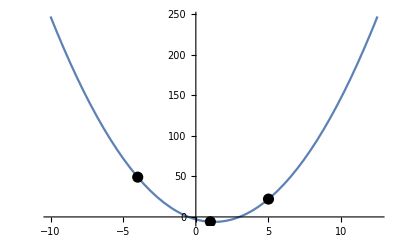

```mathematica
Plot[
2x^2-5x-3,
{x,-10,12.5},
Epilog->{
PointSize@0.02, Point[{{1,-6},{-4,49},{5,22}}]
}
]
```

```mathematica
Now
```

Fri 9 Apr 2021 13:37:08GMT-4.

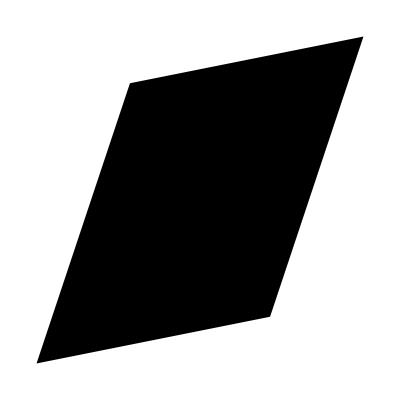

```mathematica
Graphics[
Parallelogram[{0,0},{{5,1},{2,6}}] (* lower left corner and 2 defining vectors *)
]
```

```mathematica
Area[Parallelogram[{0,0},{{5,1},{2,6}}]]
```

28

```mathematica
MatrixForm@{{5,1},{2,6}}
```

(5 | 1
2 | 6)

```mathematica
Det@{{5,1},{2,6}}
```

28

```mathematica
vectors = 
Table[
RandomInteger[{1,9},{2,2}],
3
]
```

{{{2,7},{1,7}},{{7,5},{5,7}},{{1,6},{8,9}}}

```mathematica
MatrixForm/@% (* /@ = short-hand for Map[] *)
```

{(2 | 7
1 | 7),(7 | 5
5 | 7),(1 | 6
8 | 9)}

```mathematica
matrices = 
Table[
RandomInteger[{1,9},{2,2}],
300
];
```

```mathematica
determinants = 
Map[
Det[#]&,
matrices
];
```

```mathematica
MatrixForm@matrices[[199]]
```

(1 | 2
5 | 5)

```mathematica
determinants[[199]]
```

-5

```mathematica
Now
```

Wed 14 Apr 2021 08:49:35GMT-4.

```mathematica
SeedRandom[1]
```

```mathematica
generators = RandomInteger[{-2,9},{3,3}]
```

{{-1,2,-2},{5,-2,-2},{6,4,-2}}

```mathematica
Graphics3D[
Parallelepiped[{0,0,0},generators]
]
```

-Graphics3D-

```mathematica
Volume[Parallelepiped[{0,0,0},generators]]
```

80

```mathematica
Det[{{-1,2,-2},{5,-2,-2},{6,4,-2}}]
```

-80

```mathematica
(* abolsute value of determinant gives volume*)
```

```mathematica
Det[{{a,b},{c,d}}]
```

-b c+a d

```mathematica
Det[{{a,b,c},{d,e,f},{g,h,i}}]
```

-c e g+b f g+c d h-a f h-b d i+a e i

factor
a (e i - f h) - b (d i - f g) + c (d h - e g)

```mathematica
bigMatrix = RandomInteger[{-2,9},{30,30}]
```

{{2,-1,6,3,-1,-1,-1,1,0,8,-1,4,-2,0,4,2,9,3,2,1,-2,-1,1,3,1,-2,1,0,9,1},{7,3,-1,3,0,1,7,-1,-2,2,2,-1,3,0,9,5,7,7,6,8,-2,8,8,5,2,7,0,4,1,9},{0,-1,-1,4,-1,-1,4,6,4,3,4,-2,8,5,7,-1,2,2,8,9,9,1,3,0,1,-1,0,3,9,8},{6,1,4,1,8,1,8,1,2,5,9,-2,5,9,8,5,8,1,3,3,-2,3,0,4,1,-2,8,-2,-1,5},{1,3,9,-1,4,3,9,7,7,8,0,5,9,5,2,-2,3,5,1,1,-2,7,5,-1,3,6,7,1,9,5},{-1,-1,2,3,3,2,8,7,6,0,3,6,7,-2,1,1,1,3,2,0,3,8,5,0,-1,5,-2,6,7,2},{7,7,7,-1,3,0,0,9,5,0,-2,8,4,4,5,-2,3,4,2,5,0,-2,4,3,5,6,6,9,4,2},{4,4,2,9,3,3,0,4,1,0,4,9,4,-1,7,3,5,-1,6,8,7,4,3,1,2,8,1,3,9,7},{6,0,7,6,7,5,4,9,0,7,9,-1,6,2,4,0,2,-1,5,0,5,6,-2,0,9,2,2,4,2,-1},{4,7,4,2,5,6,8,-2,5,5,9,2,0,-1,6,8,0,-1,5,-1,-2,3,6,-2,1,-2,5,8,4,-1},{8,4,2,1,3,-1,-1,8,4,0,-2,9,4,9,8,1,-2,7,6,-1,9,1,7,7,8,-2,1,-1,-2,7},{5,2,3,1,4,2,0,8,9,-2,6,0,9,8,5,2,5,3,5,8,7,6,3,1,9,5,3,5,4,9},{9,4,1,6,7,6,9,8,1,6,8,2,1,2,6,9,6,8,4,0,6,1,9,9,4,3,9,2,1,4},{3,7,8,4,3,5,0,9,6,2,0,7,3,9,0,-2,7,-1,5,-1,8,0,6,3,5,9,3,8,6,-2},{0,6,7,2,5,7,6,-1,5,9,2,6,2,0,6,3,5,4,5,9,-2,-1,-2,0,-1,2,8,8,2,6},{0,1,1,6,6,3,6,-1,4,0,6,9,5,4,0,7,6,1,-1,7,-2,-2,8,4,8,4,-1,5,3,-1},{2,6,5,5,6,9,0,7,0,6,3,-2,5,0,3,7,0,7,2,6,0,8,1,5,3,6,1,8,4,4},{5,3,4,5,8,9,3,1,7,9,6,8,0,0,-2,1,7,4,-2,1,1,-1,2,-2,4,1,6,4,6,5},{1,2,6,8,4,1,1,1,6,8,7,6,7,4,5,5,4,2,6,-1,7,-2,1,-1,4,2,5,1,5,3},{4,-1,-2,-1,2,8,6,4,2,-1,5,6,5,8,-2,-1,-1,7,-1,7,4,8,5,2,2,6,8,0,3,3},{4,8,-1,4,4,7,7,6,7,-2,-2,-1,8,8,8,-1,-1,6,0,5,3,9,2,4,-2,5,3,8,3,0},{9,9,7,8,2,0,3,9,1,5,7,5,2,0,4,0,9,1,2,2,-2,-2,-2,-1,4,5,3,-1,3,2},{-2,-2,2,2,-1,5,1,-1,3,1,-2,7,0,-2,2,-1,5,7,2,7,-1,5,8,-2,9,-2,3,6,5,-1},{8,-1,0,1,4,7,0,3,-1,0,7,4,8,9,-2,3,7,6,2,1,5,7,0,1,6,5,1,4,9,8},{-2,3,1,-1,6,7,7,6,1,3,3,6,-1,9,3,-1,5,1,0,-2,3,3,5,3,7,5,7,3,9,6},{-1,2,6,5,5,5,3,9,-1,9,1,0,9,8,5,7,0,1,1,1,7,2,-1,9,3,9,7,4,8,9},{7,5,1,6,0,9,9,7,2,8,9,8,2,1,0,1,1,-1,6,1,6,5,7,4,0,2,-2,6,2,5},{6,1,0,6,5,-1,8,5,-1,-2,9,1,1,5,0,0,-2,5,9,2,8,9,-2,7,2,5,0,9,0,-2},{9,4,1,6,7,9,7,-1,-1,4,1,8,6,-1,1,-2,2,7,-1,0,9,0,5,5,8,3,-1,7,6,6},{2,9,5,-2,9,0,-1,7,5,-1,-2,0,8,5,0,-1,4,8,6,1,6,1,0,7,-2,-1,3,5,7,1}}

```mathematica
Det[bigMatrix]//Timing
```

{0.006874,-80221515250496496604725081368300}

```mathematica
Det[
RandomInteger[{-2,9},{1000,1000}]
]//Timing
```

{31.4557,5092943139404675899932484441663778710652342729137909644057288349852140269785962235946372780628752355748188587917866838038226553508870200732548287715632715085331471072505188902613580228505072736672701159177191995665229064997412954999679458280349484125740893102260486106113997928628320089981045839577128210991145941885770475692514065294588054741334227966064918214126231423861987138560150285918588414150395088141071001101780439659988731979730866456163550514803838707800076569795763702953907502426685874447844405649601896253987615549796558876236227742609007375314693507688761154929851844221317332453149126866080906570662729937821994932066266868551403646297943246382914755360020726426231635505959036686284134333768844712297313068667523322488292451113576556150166894362032488131763617204440153507284378793046463703844007304132994754272168466637824212716269275138645712839342850021052629336128058973044326990379398308144820604197461681295130692714596708402364882711419359993275675167335719296596789320392876655882334857029499990657874711451952413687117233633544935385308777987249673190411676416621396297005131918931270204332034602341003614026272677341233873620701585879449221467247724484490429071273889965783199213600762772520546958215814277168106677390826768328577018331142151476111756312002009124033070805304430453482106735025676075661004187506221684646930941516010746875639014810794849581899710250841693718688392869469406504055496663432152017260694304811383887150651917551974967662526419004401448241220920618963857972798378292675851278087707932386883869236379007420908830055509739283561947567785435817492294378803119210237535875562914656852324022730216701794144683972426676560281129047458481038702950321715762267386008585251933495789592885207530765435331315187376794880501252609176583964153694077142310601103503779626307813048}

draw the (9,4), (8,10) pGram from the matrices03 HW

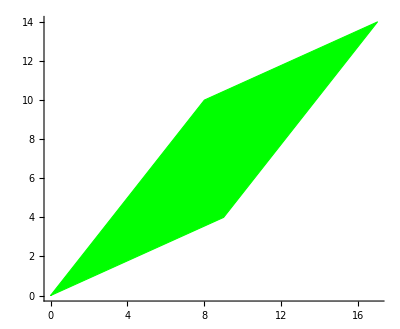

```mathematica
Graphics[
{
Green,EdgeForm@Thick,
Parallelogram[{0,0},{{9,4},{8,10}}]
},
Axes->True
]
```

```mathematica
Now
```

Mon 19 Apr 2021 08:36:34GMT-4.

```mathematica
corners = {{3,1},{6,2},{1,7},{-6,2},{-5,-5},{4,-2}}
```

{{3,1},{6,2},{1,7},{-6,2},{-5,-5},{4,-2}}

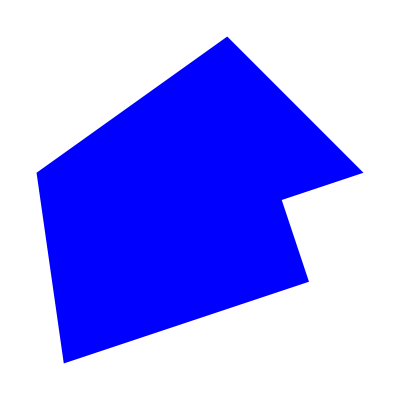

```mathematica
Graphics[
{Blue,Polygon[corners]}
]
```

```mathematica
Now
```

Tue 20 Apr 2021 11:09:45GMT-4.

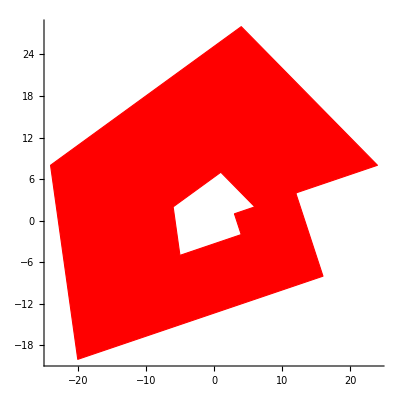

```mathematica
Graphics[
{EdgeForm@Thick,Red,Polygon[Dot[corners,{{4,0},{0,4}}]],White,Polygon[corners]},
Axes->True
]
```

```mathematica
Dot[{{3,2,1},{-4,4,4},{5,0,2}},{{6,1},{4,-3},{2,0}}]
```

{{28,-3},{0,-16},{34,5}}

```mathematica
MatrixForm@%
```

(28 | -3
0 | -16
34 | 5)

```mathematica
Flatten[{{28,-3},{0,-16},{34,5}}]
```

{28,-3,0,-16,34,5}

```mathematica
Total@%
```

48

```mathematica
Manipulate[
Graphics[
{
EdgeForm@Thick,
Red,Polygon[Dot[corners,{{h,0},{0,v}}]],
White,Polygon[corners]
},
Axes->True,
PlotRange->{{-55,55},{-70,70}}
],
{{h,4},1,9,1},
{{v,4},1,9,1}
]
```

```mathematica
Area[Polygon[Dot[corners,{{9,0},{0,7}}]]]
```

5166

```mathematica
Area[Polygon[corners]]
```

82

```mathematica
5166/82
```

63

```mathematica
Det[{{9,0},{0,7}}]
```

63

```mathematica
Now
```

Wed 21 Apr 2021 10:50:38GMT-4.

Matrices03HW

```mathematica
Tally[
Flatten[
Table[
Abs[a d - b c],
{a,0,3,1},
{b,0,3,1},
{c,0,3,1},
{d,0,3,1}
]
]
]
```

{{0,64},{1,30},{2,40},{3,42},{4,22},{6,32},{9,14},{5,6},{8,2},{7,4}}

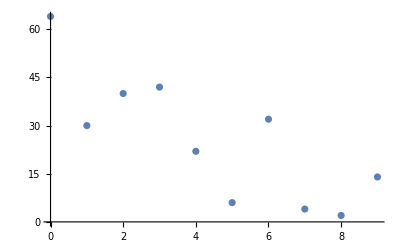

```mathematica
ListPlot[
Tally[
Flatten[
Table[
Abs[a d - b c],
{a,0,3,1},
{b,0,3,1},
{c,0,3,1},
{d,0,3,1}
]
]
]
]
```

```mathematica
vectorList = Select[
Flatten[
Table[
{a,b,c,d,Abs[a d - b c]},
{a,0,3,1},
{b,0,3,1},
{c,0,3,1},
{d,0,3,1}
],
3
],
#[[5]]==6&
]
```

{{0,2,3,0,6},{0,2,3,1,6},{0,2,3,2,6},{0,2,3,3,6},{0,3,2,0,6},{0,3,2,1,6},{0,3,2,2,6},{0,3,2,3,6},{1,2,3,0,6},{1,3,2,0,6},{1,3,3,3,6},{2,0,0,3,6},{2,0,1,3,6},{2,0,2,3,6},{2,0,3,3,6},{2,1,0,3,6},{2,2,0,3,6},{2,2,3,0,6},{2,3,0,3,6},{2,3,2,0,6},{3,0,0,2,6},{3,0,1,2,6},{3,0,2,2,6},{3,0,3,2,6},{3,1,0,2,6},{3,1,3,3,6},{3,2,0,2,6},{3,2,3,0,6},{3,3,0,2,6},{3,3,1,3,6},{3,3,2,0,6},{3,3,3,1,6}}

^this previous output tells us -- indirectly -- all the vectors that generate parallelograms with area 6.

```mathematica
Now
```

Thu 22 Apr 2021 13:57:11GMT-4.

```mathematica
Det[
{
{a,b,c},
{d,e,f},
{g,h,i}
}
]
```

-c e g+b f g+c d h-a f h-b d i+a e i

```mathematica
detOpps[2] = 3;
detOpps[3] = 14;
detOpps[n_]:=n detOpps[n-1] +2n-1
```

```mathematica
detOpps[6]
```

1955

```mathematica
Now
```

Fri 23 Apr 2021 13:44:46GMT-4.

```mathematica
{{3,1,2,4},{-6,0,0,1},{1,2,1,-3}}.{{1,1,1,0},{2,-1,-1,2},{3,1,3,3},{4,2,1,2}}
```

{{27,12,12,16},{-2,-4,-5,2},{-4,-6,-1,1}}

```mathematica
MatrixForm@%
```

(27 | 12 | 12 | 16
-2 | -4 | -5 | 2
-4 | -6 | -1 | 1)

```mathematica
Det[Out[627]]
```

Det[%627]

```mathematica
Det[{{1,8,-1},{0,4,3},{4,5,-1}}]
```

93

Let’s generate ALL the 3 x 3 matrices whose entries are integers from 1 to 9 w/ each value uese once and only once,

```mathematica
Partition[
RandomSample[
Range[1,9]
],
3
]
```

{{7,6,1},{4,5,9},{3,2,8}}

```mathematica
Det@%
```

```mathematica
117
```

Possible Options” 187, 85, 236, 120, 9, -238, 113

```mathematica
9!
```

362880

```mathematica
Permutations[Range[4]]
```

{{1,2,3,4},{1,2,4,3},{1,3,2,4},{1,3,4,2},{1,4,2,3},{1,4,3,2},{2,1,3,4},{2,1,4,3},{2,3,1,4},{2,3,4,1},{2,4,1,3},{2,4,3,1},{3,1,2,4},{3,1,4,2},{3,2,1,4},{3,2,4,1},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,1,3,2},{4,2,1,3},{4,2,3,1},{4,3,1,2},{4,3,2,1}}

```mathematica
Length@%
```

24

```mathematica
4!
```

24

```mathematica
matrices3x3 = 
Map[
Partition[#,3]&,
Permutations[Range[9]]
];
```

```mathematica
matrices3x3[[99999]](* 99,999th matrix in the list*)
```

{{3,5,8},{9,2,6},{4,1,7}}

```mathematica
Det[%]
```

-163

biggest possible determinant with these restrictions?
smallest? 
average determinant?
most common determinant?
total of the determinants?
more even or odd determinants?
ListPlot[] of values?
ListPlot[] of tallies?
Prime determinants?
fibonacci determinants?

```mathematica
Now
```

Tue 4 May 2021 13:21:01GMT-4.

```mathematica
MatrixForm@{{1,4,5,1,0,0},{3,5,5,0,1,0},{3,3,2,0,0,1}}
```

(1 | 4 | 5 | 1 | 0 | 0
3 | 5 | 5 | 0 | 1 | 0
3 | 3 | 2 | 0 | 0 | 1)

```mathematica
RowReduce[({{1, 4, 5, 1, 0, 0}, {3, 5, 5, 0, 1, 0}, {3, 3, 2, 0, 0, 1}})]
```

{{1,0,0,-5,7,-5},{0,1,0,9,-13,10},{0,0,1,-6,9,-7}}

```mathematica
MatrixForm@%
```

(1 | 0 | 0 | -5 | 7 | -5
0 | 1 | 0 | 9 | -13 | 10
0 | 0 | 1 | -6 | 9 | -7)

```mathematica
MatrixForm@{{1,4,5},{3,5,5},{3,3,2}}
```

```mathematica
({{1, 4, 5}, {3, 5, 5}, {3, 3, 2}}).{{-5,7,-5},{9,-13,10},{-6,9,-7}}
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Inverse[({{1, 4, 5}, {3, 5, 5}, {3, 3, 2}})]
```

{{-5,7,-5},{9,-13,10},{-6,9,-7}}

```mathematica
(* putting an identity matrix to the right of an original matrix yields an identity matrix to the left of the inverse matrix -- shown in written notes *)
```

```mathematica
Now
```

Tue 11 May 2021 08:53:43GMT-4.

```mathematica
matrices = Partition[#,3]&/@Permutations[Range[9]];
```

```mathematica
matrices//Length
```

362880

```mathematica
9!
```

362880

```mathematica
matrices[[123456]]
```

{{4,1,6},{5,8,9},{7,3,2}}

```mathematica
Inverse[%]
```

{{11/237,-16/237,13/79},{-53/237,34/237,2/79},{41/237,5/237,-9/79}}

```mathematica
Det@{{4,1,6},{5,8,9},{7,3,2}}
```

-237

How many of the matrices in our matrices list have inverses whose entries are entirely integers?

```mathematica
inverses = 
Map[Inverse[#]&,
matrices
];
```

Inverse::sing: Matrix {{1,2,3},{4,5,6},{7,8,9}} is singular.

Inverse::sing: Matrix {{1,2,3},{4,5,6},{9,8,7}} is singular.

Inverse::sing: Matrix {{1,2,3},{4,6,8},{5,7,9}} is singular.

General::stop: Further output of Inverse::sing will be suppressed during this calculation.

```mathematica
Select[
inverses,
AllTrue[Flatten[#],IntegerQ]&
]
```

{{{-3,1,0},{-31,13,-3},{22,-9,2}},{{-3,1,0},{44,-17,3},{-28,11,-2}},{{2,11,-9},{-2,-7,6},{1,1,-1}},2298,{{11,-12,-13},{-28,31,33},{18,-20,-21}},{{14,-19,-11},{8,-11,-6},{-27,37,21}},{{-17,19,20},{28,-31,-33},{-10,11,12}}}
 |  |  |  |

^ This previous output are the inverse matrices whose entries are integers.

```mathematica
Now
```

Thu 13 May 2021 10:49:06GMT-4.

```mathematica
matrices = Partition[#,3]&/@Permutations[Range[9]];
```

Are any of these entries in matrices “magic squares”? A matrix is “magic” if its row sums and column cums and diagonal sums are all the same.

8       1       6
3       5       7
4       9       2

```mathematica
Select[
matrices,
Total[#[[1]]]==Total[#[[2]]]==Total[#[[3]]]== (* row sums *)
#[[1]][[1]]+#[[2]][[2]]+#[[3]][[3]]== (* diagonal sums *)
#[[1]][[3]]+#[[2]][[2]]+#[[3]][[1]]==  (* other diagonal sums *)
Total[Transpose[#][[1]]]==Total[Transpose[#][[2]]]==Total[Transpose[#][[3]]]&
]
```

{{{2,7,6},{9,5,1},{4,3,8}},{{2,9,4},{7,5,3},{6,1,8}},{{4,3,8},{9,5,1},{2,7,6}},{{4,9,2},{3,5,7},{8,1,6}},{{6,1,8},{7,5,3},{2,9,4}},{{6,7,2},{1,5,9},{8,3,4}},{{8,1,6},{3,5,7},{4,9,2}},{{8,3,4},{1,5,9},{6,7,2}}}

```mathematica
MatrixForm/@%
```

{(2 | 7 | 6
9 | 5 | 1
4 | 3 | 8),(2 | 9 | 4
7 | 5 | 3
6 | 1 | 8),(4 | 3 | 8
9 | 5 | 1
2 | 7 | 6),(4 | 9 | 2
3 | 5 | 7
8 | 1 | 6),(6 | 1 | 8
7 | 5 | 3
2 | 9 | 4),(6 | 7 | 2
1 | 5 | 9
8 | 3 | 4),(8 | 1 | 6
3 | 5 | 7
4 | 9 | 2),(8 | 3 | 4
1 | 5 | 9
6 | 7 | 2)}

```mathematica
Det[#]&/@Out[7]
```

{-360,-360,360,360,360,360,-360,-360}

Use the previous logic to write a function called magicQ[] for 3x3 matrices.

```mathematica
magicQ[matrix_]:=
Total[matrix[[1]]]==Total[matrix[[2]]]==Total[matrix[[3]]]== (* row sums *)
matrix[[1]][[1]]+matrix[[2]][[2]]+matrix[[3]][[3]]== (* diagonal sums *)
matrix[[1]][[3]]+matrix[[2]][[2]]+matrix[[3]][[1]]==  (* other diagonal sums *)
Total[Transpose[matrix][[1]]]==Total[Transpose[matrix][[2]]]==Total[Transpose[matrix][[3]]];
```

```mathematica
magicQ[{{1,2,3},{4,5,6},{7,8,9}}]
```

False

```mathematica
magicQ[{{2,7,6},{9,5,1},{4,3,8}}]
```

True

```mathematica
Select[
matrices,
magicQ[#]&
]
```

{{{2,7,6},{9,5,1},{4,3,8}},{{2,9,4},{7,5,3},{6,1,8}},{{4,3,8},{9,5,1},{2,7,6}},{{4,9,2},{3,5,7},{8,1,6}},{{6,1,8},{7,5,3},{2,9,4}},{{6,7,2},{1,5,9},{8,3,4}},{{8,1,6},{3,5,7},{4,9,2}},{{8,3,4},{1,5,9},{6,7,2}}}

```mathematica
Now
```

Fri 14 May 2021 13:23:00GMT-4.

```mathematica
lucasSquare[{a_,b_,c_}]:=
{
{c-b,c+a+b,c-a},
{c-a+b,c,c+a-b},
{c+a,c-a-b,c+b}
}
```

```mathematica
lucasSquare[{7,4,2}]
```

{{-2,13,-5},{-1,2,5},{9,-9,6}}

```mathematica
MatrixForm@%
```

(-2 | 13 | -5
-1 | 2 | 5
9 | -9 | 6)

```mathematica
magicQ[Out[6]]
```

True

```mathematica
lucasSquare[{3,6,7}]
```

{{1,16,4},{10,7,4},{10,-2,13}}

```mathematica
MatrixForm@%
```

(1 | 16 | 4
10 | 7 | 4
10 | -2 | 13)

```mathematica
magicQ[%]
```

True

Based on the outputs above, some {a,b,c} triples “work” and other do not. Make a list called abcTriples that contains triples of values that will generate magic (Lucas) squares.

```mathematica
abcTriples = 
Select[
Flatten[
Table[
{a,b, c},
{a,1,10,1},
{b,1,10,1},
{c,1,10,1}
],
2
],
0<#[[1]]<#[[2]]<#[[3]]-#[[1]]&&#[[2]]≠ 2#[[1]]&
]
```

{{1,3,5},{1,3,6},{1,3,7},{1,3,8},{1,3,9},{1,3,10},{1,4,6},{1,4,7},{1,4,8},{1,4,9},{1,4,10},{1,5,7},{1,5,8},{1,5,9},{1,5,10},{1,6,8},{1,6,9},{1,6,10},{1,7,9},{1,7,10},{1,8,10},{2,3,6},{2,3,7},{2,3,8},{2,3,9},{2,3,10},{2,5,8},{2,5,9},{2,5,10},{2,6,9},{2,6,10},{2,7,10},{3,4,8},{3,4,9},{3,4,10},{3,5,9},{3,5,10},{4,5,10}}

```mathematica
lucasSquare[{1,3,5}]
```

{{2,9,4},{7,5,3},{6,1,8}}

```mathematica
lucasSquare[{1,3,6}]
```

{{3,10,5},{8,6,4},{7,2,9}}

```mathematica
Map[
MatrixForm[lucasSquare[#]]&,
abcTriples
]
```

{(2 | 9 | 4
7 | 5 | 3
6 | 1 | 8),(3 | 10 | 5
8 | 6 | 4
7 | 2 | 9),(4 | 11 | 6
9 | 7 | 5
8 | 3 | 10),(5 | 12 | 7
10 | 8 | 6
9 | 4 | 11),(6 | 13 | 8
11 | 9 | 7
10 | 5 | 12),(7 | 14 | 9
12 | 10 | 8
11 | 6 | 13),(2 | 11 | 5
9 | 6 | 3
7 | 1 | 10),(3 | 12 | 6
10 | 7 | 4
8 | 2 | 11),(4 | 13 | 7
11 | 8 | 5
9 | 3 | 12),(5 | 14 | 8
12 | 9 | 6
10 | 4 | 13),(6 | 15 | 9
13 | 10 | 7
11 | 5 | 14),(2 | 13 | 6
11 | 7 | 3
8 | 1 | 12),(3 | 14 | 7
12 | 8 | 4
9 | 2 | 13),(4 | 15 | 8
13 | 9 | 5
10 | 3 | 14),(5 | 16 | 9
14 | 10 | 6
11 | 4 | 15),(2 | 15 | 7
13 | 8 | 3
9 | 1 | 14),(3 | 16 | 8
14 | 9 | 4
10 | 2 | 15),(4 | 17 | 9
15 | 10 | 5
11 | 3 | 16),(2 | 17 | 8
15 | 9 | 3
10 | 1 | 16),(3 | 18 | 9
16 | 10 | 4
11 | 2 | 17),(2 | 19 | 9
17 | 10 | 3
11 | 1 | 18),(3 | 11 | 4
7 | 6 | 5
8 | 1 | 9),(4 | 12 | 5
8 | 7 | 6
9 | 2 | 10),(5 | 13 | 6
9 | 8 | 7
10 | 3 | 11),(6 | 14 | 7
10 | 9 | 8
11 | 4 | 12),(7 | 15 | 8
11 | 10 | 9
12 | 5 | 13),(3 | 15 | 6
11 | 8 | 5
10 | 1 | 13),(4 | 16 | 7
12 | 9 | 6
11 | 2 | 14),(5 | 17 | 8
13 | 10 | 7
12 | 3 | 15),(3 | 17 | 7
13 | 9 | 5
11 | 1 | 15),(4 | 18 | 8
14 | 10 | 6
12 | 2 | 16),(3 | 19 | 8
15 | 10 | 5
12 | 1 | 17),(4 | 15 | 5
9 | 8 | 7
11 | 1 | 12),(5 | 16 | 6
10 | 9 | 8
12 | 2 | 13),(6 | 17 | 7
11 | 10 | 9
13 | 3 | 14),(4 | 17 | 6
11 | 9 | 7
12 | 1 | 14),(5 | 18 | 7
12 | 10 | 8
13 | 2 | 15),(5 | 19 | 6
11 | 10 | 9
14 | 1 | 15)}

```mathematica
Det/@Map[
lucasSquare[#]&,
abcTriples
]
```

{-360,-432,-504,-576,-648,-720,-810,-945,-1080,-1215,-1350,-1512,-1728,-1944,-2160,-2520,-2835,-3150,-3888,-4320,-5670,-270,-315,-360,-405,-450,-1512,-1701,-1890,-2592,-2880,-4050,-504,-567,-630,-1296,-1440,-810}

```mathematica
Now
```

Mon 17 May 2021 13:18:14GMT-4.

```mathematica
lucasSquare[{2,5,9}]
```

{{4,16,7},{12,9,6},{11,2,14}}

```mathematica
MatrixForm@%
```

(4 | 16 | 7
12 | 9 | 6
11 | 2 | 14)

```mathematica
Now
```

Fri 21 May 2021 08:36:16GMT-4.

```mathematica
setDeck = 
Flatten[
Table[
{number,color,filling,shape},
{number,1,3,1},
{color,{Green,Red,Purple}},
{filling,{empty,solid,striped}},
{shape,{diamond,oval,squiggle}}
],
3
]
```

{{1,RGBColor[0, 1, 0],empty,diamond},{1,RGBColor[0, 1, 0],empty,oval},{1,RGBColor[0, 1, 0],empty,squiggle},{1,RGBColor[0, 1, 0],solid,diamond},{1,RGBColor[0, 1, 0],solid,oval},{1,RGBColor[0, 1, 0],solid,squiggle},{1,RGBColor[0, 1, 0],striped,diamond},{1,RGBColor[0, 1, 0],striped,oval},{1,RGBColor[0, 1, 0],striped,squiggle},{1,RGBColor[1, 0, 0],empty,diamond},{1,RGBColor[1, 0, 0],empty,oval},{1,RGBColor[1, 0, 0],empty,squiggle},{1,RGBColor[1, 0, 0],solid,diamond},{1,RGBColor[1, 0, 0],solid,oval},{1,RGBColor[1, 0, 0],solid,squiggle},{1,RGBColor[1, 0, 0],striped,diamond},{1,RGBColor[1, 0, 0],striped,oval},{1,RGBColor[1, 0, 0],striped,squiggle},{1,RGBColor[0.5, 0, 0.5],empty,diamond},{1,RGBColor[0.5, 0, 0.5],empty,oval},{1,RGBColor[0.5, 0, 0.5],empty,squiggle},{1,RGBColor[0.5, 0, 0.5],solid,diamond},{1,RGBColor[0.5, 0, 0.5],solid,oval},{1,RGBColor[0.5, 0, 0.5],solid,squiggle},{1,RGBColor[0.5, 0, 0.5],striped,diamond},{1,RGBColor[0.5, 0, 0.5],striped,oval},{1,RGBColor[0.5, 0, 0.5],striped,squiggle},{2,RGBColor[0, 1, 0],empty,diamond},{2,RGBColor[0, 1, 0],empty,oval},{2,RGBColor[0, 1, 0],empty,squiggle},{2,RGBColor[0, 1, 0],solid,diamond},{2,RGBColor[0, 1, 0],solid,oval},{2,RGBColor[0, 1, 0],solid,squiggle},{2,RGBColor[0, 1, 0],striped,diamond},{2,RGBColor[0, 1, 0],striped,oval},{2,RGBColor[0, 1, 0],striped,squiggle},{2,RGBColor[1, 0, 0],empty,diamond},{2,RGBColor[1, 0, 0],empty,oval},{2,RGBColor[1, 0, 0],empty,squiggle},{2,RGBColor[1, 0, 0],solid,diamond},{2,RGBColor[1, 0, 0],solid,oval},{2,RGBColor[1, 0, 0],solid,squiggle},{2,RGBColor[1, 0, 0],striped,diamond},{2,RGBColor[1, 0, 0],striped,oval},{2,RGBColor[1, 0, 0],striped,squiggle},{2,RGBColor[0.5, 0, 0.5],empty,diamond},{2,RGBColor[0.5, 0, 0.5],empty,oval},{2,RGBColor[0.5, 0, 0.5],empty,squiggle},{2,RGBColor[0.5, 0, 0.5],solid,diamond},{2,RGBColor[0.5, 0, 0.5],solid,oval},{2,RGBColor[0.5, 0, 0.5],solid,squiggle},{2,RGBColor[0.5, 0, 0.5],striped,diamond},{2,RGBColor[0.5, 0, 0.5],striped,oval},{2,RGBColor[0.5, 0, 0.5],striped,squiggle},{3,RGBColor[0, 1, 0],empty,diamond},{3,RGBColor[0, 1, 0],empty,oval},{3,RGBColor[0, 1, 0],empty,squiggle},{3,RGBColor[0, 1, 0],solid,diamond},{3,RGBColor[0, 1, 0],solid,oval},{3,RGBColor[0, 1, 0],solid,squiggle},{3,RGBColor[0, 1, 0],striped,diamond},{3,RGBColor[0, 1, 0],striped,oval},{3,RGBColor[0, 1, 0],striped,squiggle},{3,RGBColor[1, 0, 0],empty,diamond},{3,RGBColor[1, 0, 0],empty,oval},{3,RGBColor[1, 0, 0],empty,squiggle},{3,RGBColor[1, 0, 0],solid,diamond},{3,RGBColor[1, 0, 0],solid,oval},{3,RGBColor[1, 0, 0],solid,squiggle},{3,RGBColor[1, 0, 0],striped,diamond},{3,RGBColor[1, 0, 0],striped,oval},{3,RGBColor[1, 0, 0],striped,squiggle},{3,RGBColor[0.5, 0, 0.5],empty,diamond},{3,RGBColor[0.5, 0, 0.5],empty,oval},{3,RGBColor[0.5, 0, 0.5],empty,squiggle},{3,RGBColor[0.5, 0, 0.5],solid,diamond},{3,RGBColor[0.5, 0, 0.5],solid,oval},{3,RGBColor[0.5, 0, 0.5],solid,squiggle},{3,RGBColor[0.5, 0, 0.5],striped,diamond},{3,RGBColor[0.5, 0, 0.5],striped,oval},{3,RGBColor[0.5, 0, 0.5],striped,squiggle}}

```mathematica
Now
```

Mon 24 May 2021 16:31:34GMT-4.

```mathematica
setDeck=
Flatten[Table[{number,color,filling,shape},{number,1,3,1},{color,{Green,Red,Purple}},
{filling,{empty,solid,striped}},
{shape,{diamond,oval,squiggle}}],
3
];
```

Write a function called setCheck[] that takes in three different cards and returns whether or not those three cards form a set

```mathematica
setCheck[{card1_,card2_,card3_}]:= 
If[
(SameQ[card1[[1]],card2[[1]],card3[[1]]]|| UnsameQ[card1[[1]],card2[[1]],card3[[1]]])&&
(SameQ[card1[[2]],card2[[2]],card3[[2]]]|| UnsameQ[card1[[2]],card2[[2]],card3[[2]]])&&
(SameQ[card1[[3]],card2[[3]],card3[[3]]]|| UnsameQ[card1[[3]],card2[[3]],card3[[3]]])&&
(SameQ[card1[[4]],card2[[4]],card3[[4]]]|| UnsameQ[card1[[4]],card2[[4]],card3[[4]]]),
True,
 False
]
```

```mathematica
RandomSample[setDeck,3]
```

{{3,RGBColor[1, 0, 0],solid,squiggle},{1,RGBColor[0.5, 0, 0.5],empty,oval},{2,RGBColor[1, 0, 0],solid,oval}}

```mathematica
setCheck[RandomSample[setDeck,3]]
```

False

```mathematica
Tally[Table[setCheck[RandomSample[setDeck,3]],1000]]
```

{{False,987},{True,13}}

Let’s use our setCheck[] function to generate a list of all the possible sets in SET

```mathematica
allSets=Select[
Subsets[setDeck,{3}],(*generate every possible triple from the cards in setDeck*)
setCheck[#]&(*check those triples for "setness"*)
];
```

```mathematica
allSets[[777]]
```

{{1,RGBColor[0.5, 0, 0.5],striped,diamond},{2,RGBColor[1, 0, 0],empty,squiggle},{3,RGBColor[0, 1, 0],solid,oval}}

```mathematica
allSets//Length
```

1080

```mathematica
Select[allSets,
MemberQ[#,{2,Purple,striped,squiggle}]&]//Length
```

40

```mathematica
Now
```

Tue 25 May 2021 10:52:35GMT-4.

some counting reminders

```mathematica
Subsets[{leah, weston, dani, richard, pepe, mason, jason, stephanie, sophie, henry, maya, jack},{4}]//Length
```

495

```mathematica
Binomial[12,4]
```

495

why is 12 C 4 = 495?

12!/((12-4)! 4!)
12! is all the possible permutations of 12 people
(12-4)! gets groups of the correct size
4! removes all the permutations of each group of size 4

```mathematica
Graphics[{White,EdgeForm@Thick,RegularPolygon[8]}]
```

-Graphics-

```mathematica
Binomial[8,3]
```

56

There are 56 possible triangles you can make inside the polygon with 8 points

COMBINATORICS

Let’s write a function called planeMaker[] that takes in three cards (WHICH ARE NOT A SET) and generates the appropriate plane. (Recall that a plane is a 3 x 3 arrangement of 9 cards where each row, column, and diagonal forms a set.)

```mathematica
planeMaker[{c1_,c2_,c4_}]:=
{
c1,
c2,
setCompleter[c1,c2],
c4,
c5,
c6,
c7,
c8,
c9
}
```

```mathematica
{1,Purple,striped,squiggle},{2,Purple,empty,diamond}
```

```mathematica
Now
```

Wed 26 May 2021 13:23:18GMT-4.

In order to write planeMaker[], we need a function called setCompleter[] that takes in two cards and returns the third card that... completes the set.

```mathematica
setCompleter[{card1_,card2_}]:=
With[
{
number = {1,2,3},color = {Green,Purple,Red},
filling = {empty, striped, solid},
shape = {diamond, oval, squiggle}
},
newNumber = 
If[
SameQ[card1[[1]],card2[[1]]],(* if the number attributes are the same*)
card1[[1]],(*return that atribute *)
Complement[number,{card1[[1]],card2[[1]]}] (*otherwise, return the missing one*)
];
newColor = 
If[
SameQ[card1[[2]],card2[[2]]],
card1[[2]],
Complement[color,{card1[[2]],card2[[2]]}]
];
newFilling = 
If[
SameQ[card1[[3]],card2[[3]]],
card1[[3]],
Complement[filling,{card1[[3]],card2[[3]]}]
];
newShape = 
If[
SameQ[card1[[4]],card2[[4]]],
card1[[4]],
Complement[shape,{card1[[4]],card2[[4]]}]
];
Flatten@{newNumber,newColor,newFilling,newShape}
]
```

```mathematica
setCompleter[{{2,Purple,striped,squiggle},{3,Red,striped,oval}}]
```

{1,RGBColor[0, 1, 0],striped,diamond}

```mathematica
RandomSample[setDeck,2]
```

{{3,RGBColor[1, 0, 0],solid,oval},{2,RGBColor[0, 1, 0],solid,squiggle}}

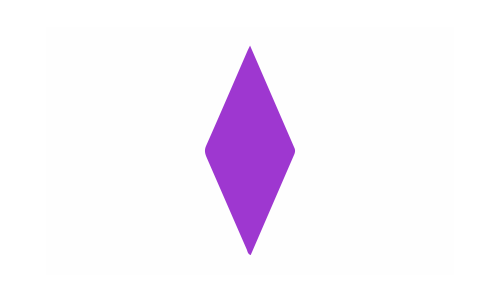

```mathematica
setCards[setCompleter[%]]
```

```mathematica
Binomial[81,2]
```

3240

We’re now ready to write planeMaker[]

```mathematica
planeMaker[{c1_,c2_,c4_}]:=
Partition[
{
c1,
c2,
setCompleter[{c1,c2}], (* c3 *)
c4,
setCompleter[{setCompleter[{c1,c2}],setCompleter[{c1,c4}]}],(* c5 *)
setCompleter[{c4,setCompleter[{setCompleter[{c1,c2}],setCompleter[{c1,c4}]}]}],
setCompleter[{c1,c4}],(* c7 *)
setCompleter[{c2,setCompleter[{setCompleter[{c1,c2}],setCompleter[{c1,c4}]}]}],
setCompleter[{c1,setCompleter[{setCompleter[{c1,c2}],setCompleter[{c1,c4}]}]}]
},
3
]
```

```mathematica
planeMaker[{{1,Red,striped,oval},{2,Purple,striped,squiggle},{2,Red,empty,diamond}}]
```

{{{1,RGBColor[1, 0, 0],striped,oval},{2,RGBColor[0.5, 0, 0.5],striped,squiggle},{3,RGBColor[0, 1, 0],striped,diamond}},{{2,RGBColor[1, 0, 0],empty,diamond},{3,RGBColor[0.5, 0, 0.5],empty,oval},{1,RGBColor[0, 1, 0],empty,squiggle}},{{3,RGBColor[1, 0, 0],solid,squiggle},{1,RGBColor[0.5, 0, 0.5],solid,diamond},{2,RGBColor[0, 1, 0],solid,oval}}}

In order to visualize these as cards, create a function called setToImage[]

```mathematica
setToImage[set_]:=Map[setCards[#]&,set]
```

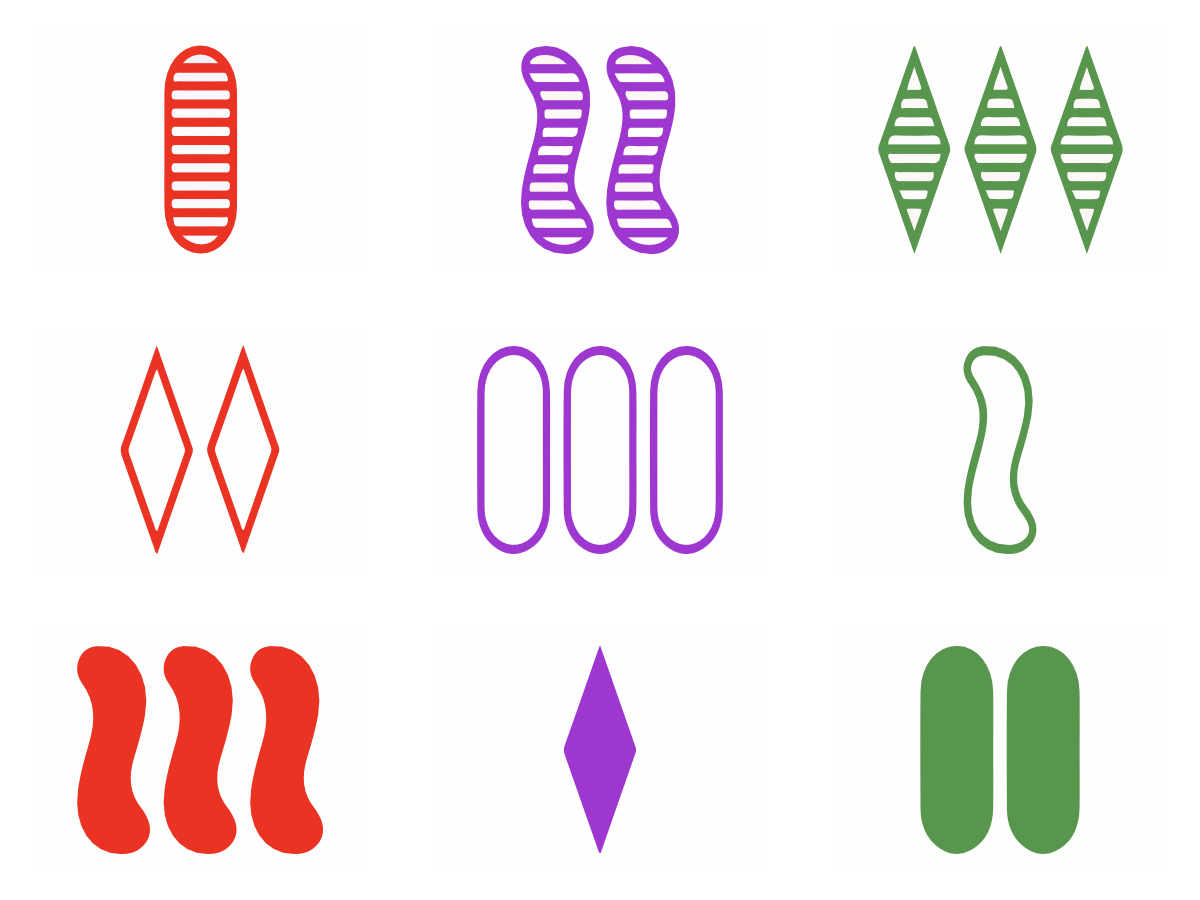

```mathematica
Map[
setToImage[#]&,
planeMaker[{{1,Red,striped,oval},{2,Purple,striped,squiggle},{2,Red,empty,diamond}}]
]//TableForm
```

```mathematica
Now
```

Thu 27 May 2021 13:23:15GMT-4.

```mathematica
allSets[[423]]
```

{{1,RGBColor[1, 0, 0],empty,squiggle},{2,RGBColor[0.5, 0, 0.5],solid,oval},{3,RGBColor[0, 1, 0],striped,diamond}}

find all the red sets

```mathematica
setToImage/@Select[
allSets,
#[[1]][[4]]==squiggle&&#[[2]][[4]]==squiggle&&#[[3]][[4]]==squiggle&
];
```

```mathematica
Select[
setDeck,
#[[3]]==striped&&#[[4]]==squiggle&
]
```

{{1,RGBColor[0, 1, 0],striped,squiggle},{1,RGBColor[1, 0, 0],striped,squiggle},{1,RGBColor[0.5, 0, 0.5],striped,squiggle},{2,RGBColor[0, 1, 0],striped,squiggle},{2,RGBColor[1, 0, 0],striped,squiggle},{2,RGBColor[0.5, 0, 0.5],striped,squiggle},{3,RGBColor[0, 1, 0],striped,squiggle},{3,RGBColor[1, 0, 0],striped,squiggle},{3,RGBColor[0.5, 0, 0.5],striped,squiggle}}

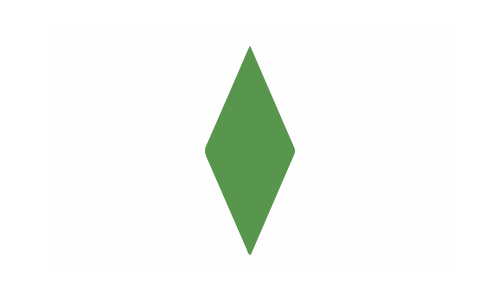
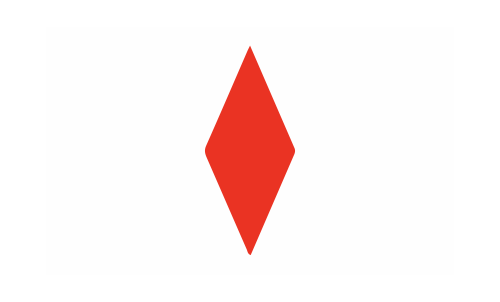
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
setCards/@allSets[[123]]
```

Let’s brute force a counting of all the planes in a set deck. A plane is generated by three cards that DO NOt form a set. How many such triples are there? (That is, three cards the DON’T form a set).

```mathematica
notSets = Select[
Subsets[setDeck,{3}],
!setCheck[#]&
];
```

```mathematica
Length[notSets]
```

84240

```mathematica
Binomial[81,3]-1080
```

84240

Even though these triples are too numerous, let’s Map[] our planMaker[] function across all of them.

```mathematica
Map[
Sort[Flatten[planeMaker[#],1]]&,
notSets
]
```

{{{1,RGBColor[0, 1, 0],empty,diamond},{1,RGBColor[0, 1, 0],empty,oval},{1,RGBColor[0, 1, 0],empty,squiggle},{1,RGBColor[0, 1, 0],solid,diamond},{1,RGBColor[0, 1, 0],solid,oval},{1,RGBColor[0, 1, 0],solid,squiggle},{1,RGBColor[0, 1, 0],striped,diamond},{1,RGBColor[0, 1, 0],striped,oval},{1,RGBColor[0, 1, 0],striped,squiggle}},84238,{{3,RGBColor[1, 0, 0],empty,diamond},{3,RGBColor[1, 0, 0],empty,oval},{3,RGBColor[1, 0, 0],empty,squiggle},4,{3,RGBColor[1, 0, 0],striped,oval},{3,RGBColor[1, 0, 0],striped,squiggle}}}
 |  |  |  |

```mathematica
DeleteDuplicates[
Map[
Sort[Flatten[planeMaker[#],1]]&,
notSets
]
]//Length
```

1170

```mathematica
Now
```

Wed 2 Jun 2021 08:34:33GMT-4.

```mathematica
attributeCount[set_]:=
Count[ (* counting the number of attributes that are different in a given set *)
Table[
SameQ[set[[1]][[n]], set[[2]][[n]]],
{n,1,4,1}
],
False
]
```

```mathematica
allSets[[432]]
```

{{1,RGBColor[0.5, 0, 0.5],solid,diamond},{2,RGBColor[0, 1, 0],solid,diamond},{3,RGBColor[1, 0, 0],solid,diamond}}

```mathematica
attributeCount[allSets[[432]]]
```

2

```mathematica
allSets[[111]]
```

{{1,RGBColor[0, 1, 0],empty,squiggle},{2,RGBColor[1, 0, 0],empty,oval},{3,RGBColor[0.5, 0, 0.5],empty,diamond}}

```mathematica
attributeCount[allSets[[111]]]
```

3

```mathematica
attributeCount[allSets[[476]]]
```

4

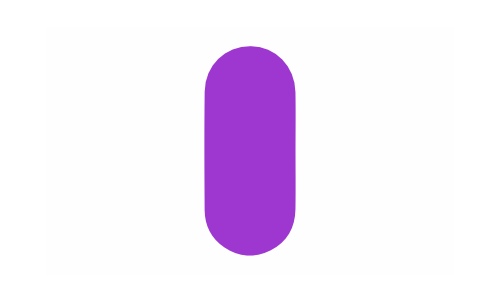
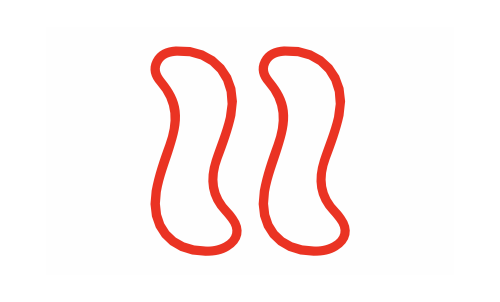
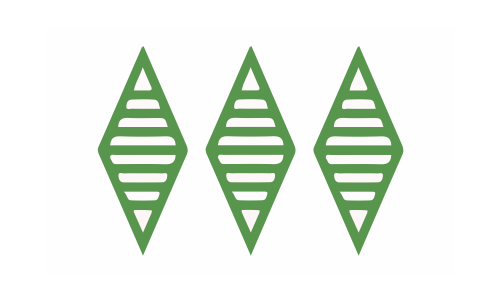

```mathematica
setCards/@allSets[[476]]
```

```mathematica
attributeCount[allSets[[526]]]
```

1

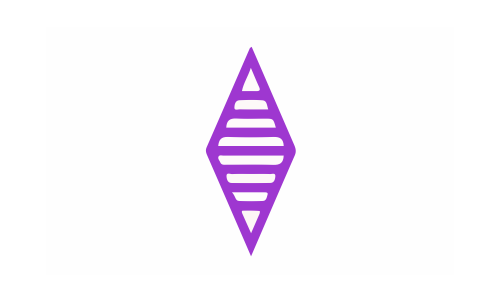
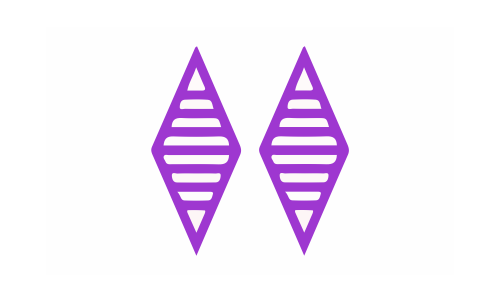
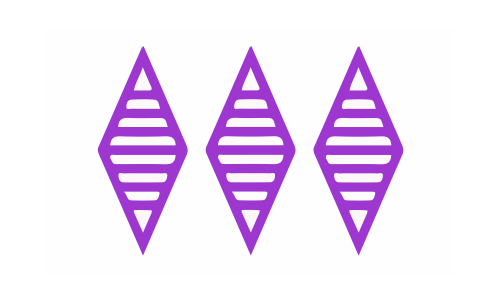

```mathematica
setCards/@allSets[[526]]
```

Since attributeCount[] returns a number, what’s this doing?

```mathematica
Select[
allSets,
attributeCount[#]==1&
];
```

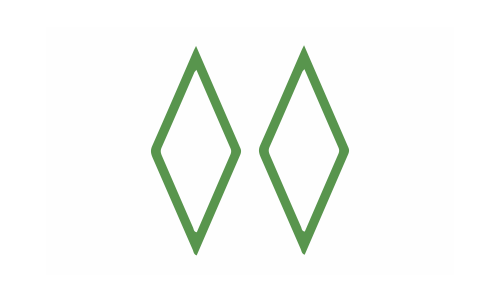
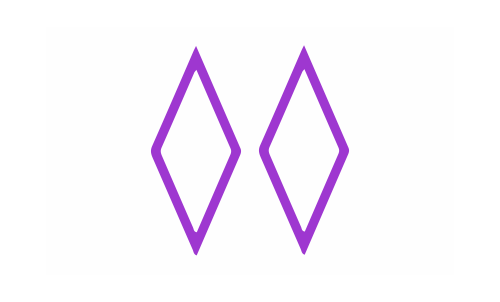
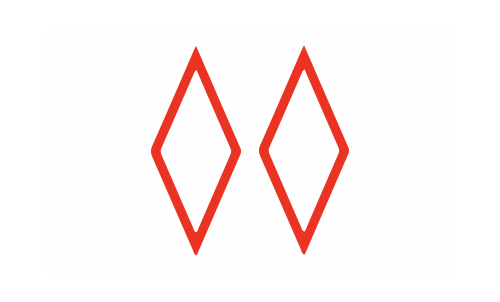

```mathematica
setCards/@{{2,RGBColor[0, 1, 0],empty,diamond},{2,RGBColor[0.5, 0, 0.5],empty,diamond},{2,RGBColor[1, 0, 0],empty,diamond}}
```

```mathematica
Table[
Select[
allSets,
attributeCount[#]==numberDifferent&
]//Length,
{numberDifferent,1,4,1}
]
```

{108,324,432,216}

```mathematica
Now
```

Fri 4 Jun 2021 10:49:14GMT-4.

```mathematica
Select[
Table[RandomSample[setDeck,3],10000], (* 10000 = how many times it runs*)
setCheck[#]&
]//Length
```

115

```mathematica
N[115/10000,8]
```

0.0115

```mathematica
N[1/79,8]
```

0.012658228

```mathematica
SortBy[
Tally[
Table[
Select[
Subsets[
RandomSample[setDeck,12], (* checks for sets in group of 12 cards *)
{3}
],
setCheck[#]&
]//Length, (* amount of sets *)
1000 (* gives number of sets 1000 times *)
]
],
#[[1]]&
]//TableForm
```

0 | 29
1 | 148
2 | 272
3 | 290
4 | 161
5 | 77
6 | 22
7 | 1